## Supermodes in function of bare modes

```mathematica
e1=Symbol["e1"];
e2=Symbol["e2"];
e3=Symbol["e3"];
```

```mathematica
ε[1]=1/2(e1 - √2 e2 + e3);
ε[2]=1/(√2)(-e1 + e3);
ε[3]=1/2(e1 + √2 e2 + e3);
```

```mathematica
overlapRules={e1 e3->0, e1 e2->0, e2 e3->0};
```

```mathematica
Integrand[α_,β_,γ_,μ_]:=(Conjugate[ε[μ]]ε[α])×(Conjugate[ε[β]]ε[γ]);
```

```mathematica
f[α_,β_,γ_,μ_]:=Simplify[ComplexExpand[Integrand[α,β,γ,μ]],Assumptions->{e1*e3==0,e1*e2==0,e2*e3==0}]
```

```mathematica
fnorm[α_,β_,γ_,μ_]:=f[α,β,γ,μ]/f[2,2,2,2];
```

```mathematica
Matrix=({{fnorm[1,1,1,1], fnorm[2,2,1,1], fnorm[3,3,1,1], fnorm[2,3,2,1]}, {fnorm[1,1,2,2], fnorm[2,2,2,2], fnorm[3,3,2,2], fnorm[1,2,3,2]}, {fnorm[1,1,3,3], fnorm[2,2,3,3], fnorm[3,3,3,3], fnorm[2,1,2,3]}});
Matrix/.{e1^4->A,e2^4->A,e3^4->A}//MatrixForm
```

(3/4 | 1/2 | 3/4 | 1/2
1/2 | 1 | 1/2 | 1/2
3/4 | 1/2 | 3/4 | 1/2)

```mathematica
PhaseShifts={Matrix[[1,1]]+2*Matrix[[1,3]], 2*Matrix[[2,1]]+2*Matrix[[2,3]],2*Matrix[[3,1]]+Matrix[[3,3]]};
```

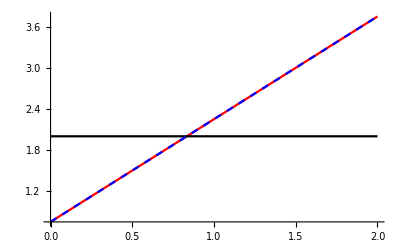

```mathematica
Plot[PhaseShifts/.{e1^4->A,e2^4->α A,e3^4->A}//Evaluate,{α,0,2},PlotStyle->{Red,Black,{Blue,Dashed}}]
```

## Light distribution 3 rings

```mathematica
ClearAll[J,ω0,ω1,ω2,ω3,Ω]
Ω=({{ω1, -J, 0}, {-J, ω2, -J}, {0, -J, ω3}});
ωbAS=Eigenvalues[Ω][[3]];
ωbC=Eigenvalues[Ω][[2]];
ωbS=Eigenvalues[Ω][[1]];
```

```mathematica
aAS=Eigenvectors[Ω][[3]];
aC=Eigenvectors[Ω][[2]];
aS=Eigenvectors[Ω][[1]];
```

```mathematica
ωbC
```

Root[J^2 ω1+J^2 ω3-ω1 ω2 ω3+(-2 J^2+ω1 ω2+ω1 ω3+ω2 ω3) #1+(-ω1-ω2-ω3) #1^2+#1^3&,2]

```mathematica
SetOptions[Plot,{Frame->True}];
```

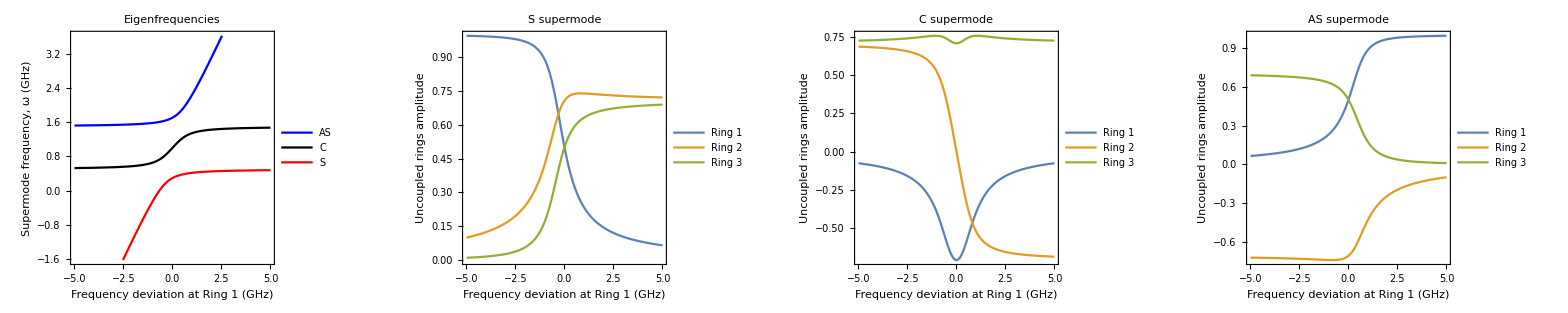

```mathematica
rnum={ω1-> 1.0+δ,ω2-> 1.0,ω3-> 1.0,J-> .5};
plt0=Plot[{ωbAS,ωbC,ωbS}/.rnum//Evaluate,{δ,-5,5},PlotStyle->{Blue,Black,Red},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Supermode frequency, ω (GHz)"},PlotLabel->"Eigenfrequencies",PlotLegends->Placed[{"AS", "C", "S"},{0.75,0.2}]];
plt1=Plot[(aS/Norm[aS])/.rnum//Evaluate,{δ,-5,5},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Uncoupled rings amplitude"},PlotLabel->"S supermode",PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.25}]];
plt2=Plot[(aC/Norm[aC])/.rnum//Evaluate,{δ,-5,5},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Uncoupled rings amplitude"},PlotLabel->"C supermode",PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.25}]];
plt3=Plot[(aAS/Norm[aAS])/.rnum//Evaluate,{δ,-5,5},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Uncoupled rings amplitude"},PlotLabel->"AS supermode",PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.2}]];
Grid[{{plt0,plt1,plt2,plt3}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]
```

```mathematica
c=299792458;
ω0exp =2*Pi c/(1560×10^-9);
Jexp = 2Pi  (10×10^9)/(√2);
κ = 5.35×10^9;
```

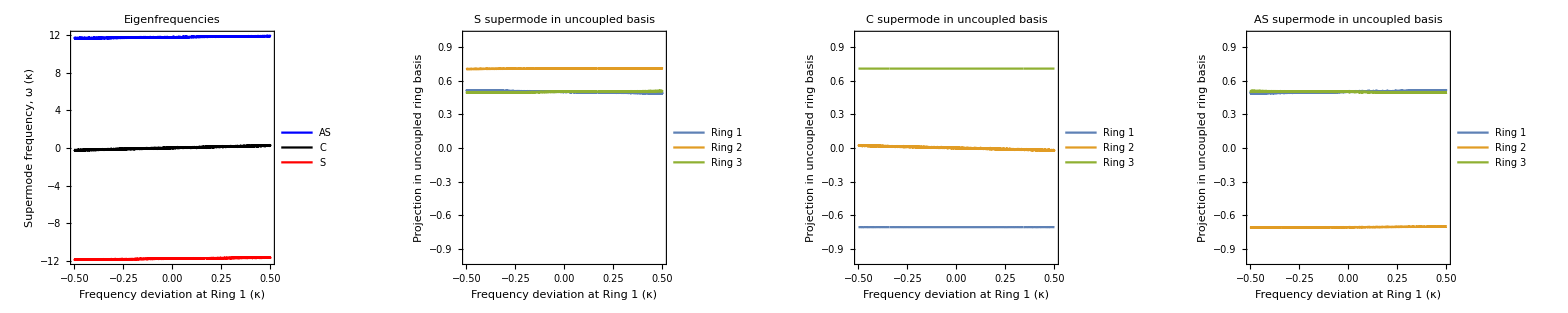

```mathematica
rnum={ω1-> ω0exp+ δ×κ,ω2-> ω0exp,ω3-> ω0exp,J-> Jexp};
plt0=Plot[({ωbAS,ωbC,ωbS}-ω0exp)/κ/.rnum//Evaluate,{δ,-.5,.5},PlotStyle->{Blue,Black,Red},FrameLabel->{"Frequency deviation at Ring 1 (κ)","Supermode frequency, ω (κ)"},PlotLabel->"Eigenfrequencies",PlotLegends->Placed[{"AS", "C", "S"},{0.75,0.25}]];
plt1=Plot[(aS/Norm[aS])/.rnum//Evaluate,{δ,-.5,.5},FrameLabel->{"Frequency deviation at Ring 1 (κ)","Projection in uncoupled ring basis"},PlotLabel->"S supermode in uncoupled basis",PlotRange->{Automatic, {-1,1}}, PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.2}]];
plt2=Plot[(aC/Norm[aC])/.rnum//Evaluate,{δ,-.5,.5},FrameLabel->{"Frequency deviation at Ring 1 (κ)","Projection in uncoupled ring basis"},PlotLabel->"C supermode in uncoupled basis",PlotRange->{Automatic, {-1,1}},PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.2}]];
plt3=Plot[(aAS/Norm[aAS])/.rnum//Evaluate,{δ,-.5,.5},FrameLabel->{"Frequency deviation at Ring 1 (κ)","Projection in uncoupled ring basis"},PlotLabel->"AS supermode in uncoupled basis",PlotRange->{Automatic, {-1,1}},PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.2}]];
Grid[{{plt0,plt1,plt2,plt3}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]
```

```mathematica
κ/Jexp//N
```

0.120417

## Dynamic phase-shifts

```mathematica
ClearAll[J,ω0,ω1,ω2,ω3,Ω]
(*Ω=({{ω0exp+ δ×κ, -Jexp, 0}, {-Jexp, ω0exp, -Jexp}, {0, -Jexp, ω0exp}});*)
Ω=({{ω0+δ, -J, 0}, {-J, ω0, -J}, {0, -J, ω0}});
ωbAS=Eigenvalues[Ω][[3]];
ωbC=Eigenvalues[Ω][[2]];
ωbS=Eigenvalues[Ω][[1]];
aAS=Eigenvectors[Ω][[3]];
aC=Eigenvectors[Ω][[2]];
aS=Eigenvectors[Ω][[1]];
```

```mathematica
c=299792458;
ω0exp =2*Pi c/(1560×10^-9);
Jexp = 2Pi  (10×10^9)/(√2);
κ = 5.35×10^9;
```

```mathematica
(*rnum={ω1-> ω0exp+ δ×κ,ω2-> ω0exp,ω3-> ω0exp,J-> Jexp};)
```

```mathematica
e1=Symbol["e1"];
e2=Symbol["e2"];
e3=Symbol["e3"];
```

```mathematica
ε[1]=(aS/Norm[aS]). {e1,e2,e3};
ε[2]=(aC/Norm[aC]). {e1,e2,e3};
ε[3]=(aAS/Norm[aAS]). {e1,e2,e3};
```

```mathematica
overlapRules={e1 e3->0, e1 e2->0, e2 e3->0};
```

```mathematica
Integrand[α_,β_,γ_,μ_]:=(Conjugate[ε[μ]]ε[α])×(Conjugate[ε[β]]ε[γ]);
```

```mathematica
f[α_,β_,γ_,μ_]:=Simplify[ComplexExpand[Integrand[α,β,γ,μ]],Assumptions->{e1*e3==0,e1*e2==0,e2*e3==0}]
```

```mathematica
fnorm[α_,β_,γ_,μ_]:=f[α,β,γ,μ]/f[2,2,2,2];
```

```mathematica
Matrix=({{fnorm[1,1,1,1], fnorm[2,2,1,1], fnorm[3,3,1,1], fnorm[2,3,2,1]}, {fnorm[1,1,2,2], fnorm[2,2,2,2], fnorm[3,3,2,2], fnorm[1,2,3,2]}, {fnorm[1,1,3,3], fnorm[2,2,3,3], fnorm[3,3,3,3], fnorm[2,1,2,3]}})/.{e1^4->A,e2^4-> A,e3^4->A}/.{δ->0}//MatrixForm
```

```mathematica
fnorm[1,2,2,2]/.{e1^4->A,e2^4-> A,e3^4->A}/.{δ->0}//N
```

((2. J^4-1. J^2 ω0^2+ω0^4+Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^4+2. ω0 (J^2-2. ω0^2) Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]-1. (J^2-6. ω0^2) Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2-4. ω0 Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^3+Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^4+Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2 (3. J^2+2. ω0^2-4. ω0 Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]+2. Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2))^2 (A J^8+A J^4 (ω0-(0.+1. ⅈ) Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]-1. Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]) (ω0+(0.+1. ⅈ) Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]-1. Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]])^2 (ω0-1. Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,1])+A (J^2-1. ω0^2+Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2-(0.+2. ⅈ) Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]] (ω0-1. Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]])+2. ω0 Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]-1. Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2)^2 (J^2-1. ω0^2+Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2+(0.+2. ⅈ) Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]] (ω0-1. Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]])+2. ω0 Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]-1. Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2) (J^2-1. ω0^2+2. ω0 Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,1]-1. Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,1]^2)))/(J^8 (1/J^4(2. J^4-1. J^2 ω0^2+ω0^4+Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^4+2. ω0 (J^2-2. ω0^2) Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]-1. (J^2-6. ω0^2) Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2-4. ω0 Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^3+Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^4+Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2 (3. J^2+2. ω0^2-4. ω0 Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]+2. Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2)))^(3/2) (A J^8+A J^4 (Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2+(ω0-1. Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]])^2)^2+A (Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^4+(-1. J^2+ω0^2-2. ω0 Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]+Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2)^2+2. Im[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2 (J^2+ω0^2-2. ω0 Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]+Re[Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,2]]^2))^2) √((2. J^4+J^2 ω0^2-2. J^2 ω0 Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,1]+J^2 Root[2 J^2 ω0-ω0^3+(-2 J^2+3 ω0^2) #1-3 ω0 #1^2+#1^3&,1]^2)/J^4))

```mathematica
Plot[f[1,1,1,1]/.rnum/.{e1^4->1,e2^4-> 1,e3^4->1},{δ,0,1}]
```

```mathematica
PhaseShifts={fnorm[1,1,1,1]+2*fnorm[2,2,1,1], 2*fnorm[1,1,2,2]+2*fnorm[3,3,2,2],2*fnorm[1,1,3,3]+fnorm[3,3,3,3]}/.rnum/.{e1^4->1,e2^4-> 1,e3^4->1};
```

```mathematica
Plot[{fnorm[1,1,1,1]+2*fnorm[2,2,1,1], 2*fnorm[1,1,2,2]+2*fnorm[3,3,2,2],2*fnorm[1,1,3,3]+fnorm[3,3,3,3]}/.rnum/.{e1^4->1,e2^4-> 1,e3^4->1}//Evaluate, {δ, -10, 10}]
```